```mathematica
{100,181,205}/255//N
```

{0.392157,0.709804,0.803922}

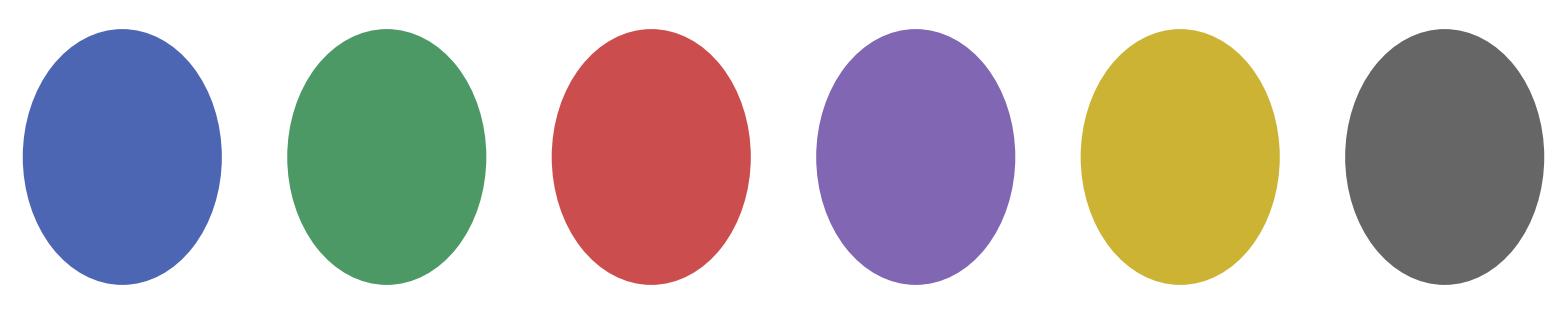

```mathematica
sns={RGBColor[.3,.4,.7],RGBColor[.3,.6,.4],RGBColor[0.8,0.3,0.3],RGBColor[0.5,0.4,0.7],RGBColor[0.8,0.7,0.2],RGBColor[0.4,0.4,0.4]};
GraphicsRow[Graphics/@({#,Disk[{0,0}]}&/@sns)]
```

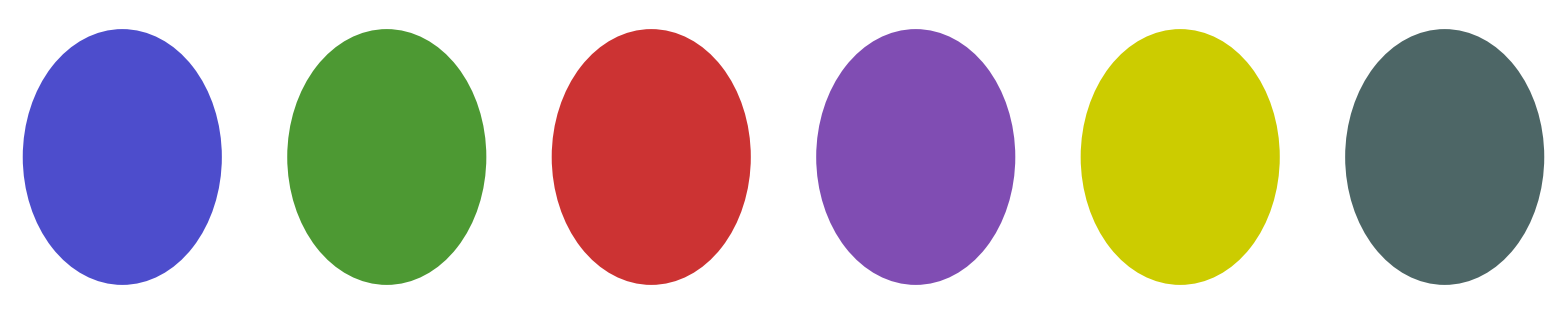

```mathematica
john = {RGBColor[.3,.3,.8],RGBColor[.3,.6,.2],RGBColor[0.8,0.2,0.2],RGBColor[0.5,0.3,0.7],RGBColor[0.8,0.8,0.0],RGBColor[0.3,0.4,0.4]};
GraphicsRow[Graphics/@({#,Disk[{0,0}]}&/@john)]
```

```mathematica
rgbtohex=ToUpperCase[
StringJoin[
IntegerString[IntegerPart/@(List@@#*255),16]
]
]&
```

ToUpperCase[StringJoin[IntegerString[IntegerPart/@(List@@#1 255),16]]]&

```mathematica
rgbtohex/@john
```

{4C4CCC,4C9933,CC3333,7F4CB2,CCCC0,4C6666}

21394.5